calculating the angle required for the MOT beams to clear the parabolic mirror with a desired minimum distance.  this is just a rough estimate, as I treated the parabolic surface as spherical for the geometrical calculation. I also ignored the chamfer on the parabolic mirror so this is a more conservative estimate (i.e. beam clearance should be slightly better than predicted here)

See my sketches on page 226 of my turquoise Leuchtturm1917 journal.

```mathematica
Clear[θ]
f=5.26;(*mirror focal length*)
R=f; (*radius of circle touching mirror edges*)
h=8.1;(*mirror clear aperture dia.*)
d=(h/2)^2/(4 f);(*mirror depth*)
dh=(9-8.1)/2;(*mirror border thickness, radially*)
w0=0.52;(*beam waist*)
NSolve[h-R √((1-Cos[θ])^2+Sin[θ]^2)==0,θ,Reals]
```

NSolve::ratnz: NSolve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{θ→ConditionalExpression[1. (-1.75756+6.28319 C[1]), C[1]∈ℤ]},{θ→ConditionalExpression[1. (1.75756+6.28319 C[1]), C[1]∈ℤ]}}

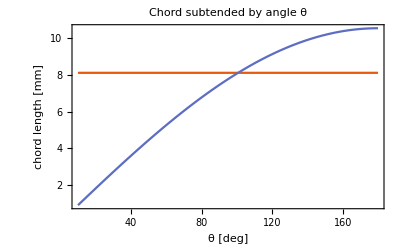

```mathematica
Plot[{h,R √((1-Cos[π/180 θ])^2+Sin[π/180 θ]^2)},{θ,10,180},PlotLabel->"Chord subtended by angle θ",PlotTheme->"Scientific",FrameLabel->{"θ [deg]", "chord length [mm]"}]
```

The chord subtended by this angle doesn’t agree with the angle spanned given the NA of the system. not sure what’s up...

```mathematica
NA=Sin[ArcTan[h/(2 f)]]
```

0.610075

```mathematica
2*ArcSin[NA]*180/π
```

75.1898

Can just say that dR must be about 0.5 mm, bc R is about (9 - 8.1)/2.

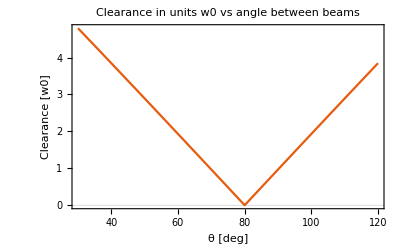

```mathematica
dR=0.5;
θ=100;
Plot[((R+dR)√((1-Cos[(π-π/180(θ+Θ))/2])^2+Sin[(π-π/180(θ+Θ))/2]^2))/w0,{Θ,30,120},PlotRange->All,PlotLabel->"Clearance in units w0 vs angle between beams",PlotTheme->"Scientific",FrameLabel->{"θ [deg]", "Clearance [w0]"}]
```

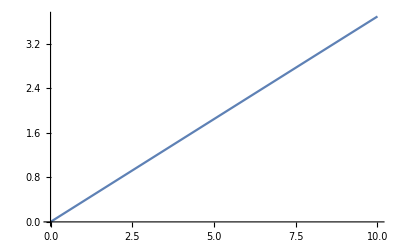

```mathematica
Plot[((R+dR)√((1-Cos[π/180 α])^2+Sin[π/180 α]^2))/w0,{α,0,10}]
```

beam separation angle

```mathematica
2*(90-θ/2-α)/.α->6
```

122.74

```mathematica
Series[√(r^2-x^2),{x,0,3}]
```

√(r^2)-x^2/(2 √(r^2))+O[x]^4